## Next steps for Dean

### Make functions

Use this function:

```mathematica
Table[NestGraph[ReplaceList[{
{left___,0,0,s___}:>{left,s,1,0,0},
{left___,1,0,s___}:>{left,s,0,1},
{left___,0,1,s___}:>{left,s,1,1,0},
{left___,1,1,s___}:>{left,s,0,1}}],{{1,1}},i,VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),GraphLayout->"LayeredDigraphEmbedding",PerformanceGoal->"Quality"],{i,1,8}]
```

James’ crude function:

```mathematica
MultiwayTagSystem[rule_,init_,t_]:=NestGraph[rule,init,t,VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),GraphLayout->"LayeredDigraphEmbedding",PerformanceGoal->"Quality"]
```

```mathematica
MultiwayTagSystem[ReplaceList[{
{left___,0,0,s___}:>{left,s,1,0,0},
{left___,1,0,s___}:>{left,s,0,1},
{left___,0,1,s___}:>{left,s,1,1,0},
{left___,1,1,s___}:>{left,s,0,1}}],
{{1,1}},
8
]
```

-Graphics-

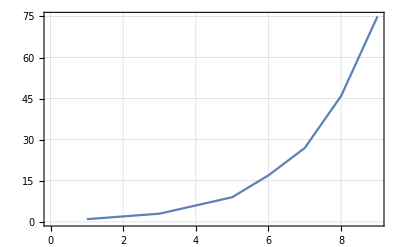

```mathematica
ListLinePlot[Table[
Length[

Complement[

VertexList[MultiwayTagSystem[ReplaceList[{
{left___,0,0,s___}:>{left,s,1,0,0},
{left___,1,0,s___}:>{left,s,0,1},
{left___,0,1,s___}:>{left,s,1,1,0},
{left___,1,1,s___}:>{left,s,0,1}}],
{{1,1}},
t
]],

VertexList[MultiwayTagSystem[ReplaceList[{
{left___,0,0,s___}:>{left,s,1,0,0},
{left___,1,0,s___}:>{left,s,0,1},
{left___,0,1,s___}:>{left,s,1,1,0},
{left___,1,1,s___}:>{left,s,0,1}}],
{{1,1}},
t-1
]]


]],{t,2,10}],PlotTheme->"Detailed"]
```

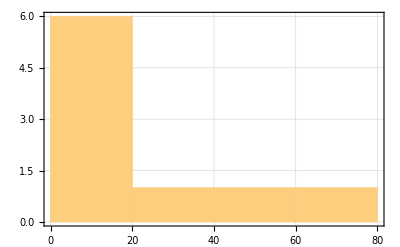

```mathematica
Histogram[Table[
Length[

Complement[

VertexList[MultiwayTagSystem[ReplaceList[{
{left___,0,0,s___}:>{left,s,1,0,0},
{left___,1,0,s___}:>{left,s,0,1},
{left___,0,1,s___}:>{left,s,1,1,0},
{left___,1,1,s___}:>{left,s,0,1}}],
{{1,1}},
t
]],

VertexList[MultiwayTagSystem[ReplaceList[{
{left___,0,0,s___}:>{left,s,1,0,0},
{left___,1,0,s___}:>{left,s,0,1},
{left___,0,1,s___}:>{left,s,1,1,0},
{left___,1,1,s___}:>{left,s,0,1}}],
{{1,1}},
t-1
]]


]],{t,2,10}],5,PlotTheme->"Detailed"]
```

Coding challenge: Create RandomMutliwayTagSystem function (repurposing the code for RandomPathCanyons)

### Generate 5 (interesting!) multiway tag systems

What does ‘interesting’ mean?

I would recommend selecting multiway tag systems based on interesting multiway behavior.

Macro-level point: we want to explore the relationship between multiway and singleway behavior

We know that there are different singleway behaviors (explosive, degenerate, periodic)

The question is: what is the correspondence (if any) between singleway and multiway behavior?

An example of singleway-multiway behavior comparisons: are all singleway paths in a multiway system similar in behavior?

### Compare behaviors of different paths

Behaviors to consider: 1) generation plot; 2) ListLinePlot of lengths; 3) state transition graphs

### Study multiway behavior

1) branchial graphs (and ArrayPlot[GraphDistanceMatrix[]] for branchial graphs); 2) confluence; 3) (non-cumulative) growth rate (ListLinePlot and Histogram)

## Notebook Template

## Top of the notebook: functions

Example:

```mathematica
MultiwayTagSystem[rule_,init_,t_]:=NestGraph[rule,init,t,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",PerformanceGoal->"Quality"]
```

## 5 ‘sections’ for 5 different multiway tag systems

## Example

### Section 1.A: Multiway tag system example

### Section 1.B: Multiway behaviors

### Section 1.C: Singleway behaviors (for all paths)

### Section 1.D: Analysis

#### ‘Why I selected this multiway tag system’

#### Observed relationship between singleway and multiway behavior

### Repeat for sections 2-5